```mathematica
Quit[];
```

```mathematica
ScalarMSF0[m_,s_]:=2-2Log[m]-(2 √(4 m^2-s))/(√s)ArcTan[(√s)/(√(4 m^2-s))];
ScalarMSF1[m_,s_]:=2-2Log[m]+(2 √(4 m^2-s))/(√s)(ArcTan[-(√s)/(√(4 m^2-s))]+π);
```

```mathematica
InitialGuessSPScalar0[M_,m_,c_,c2_]:=M^2-c×ScalarMSF0[m,M^2]-ⅈ×c2;
InitialGuessSPScalar1[M_,m_,c_,c2_]:=M^2-c×ScalarMSF1[m,M^2]-ⅈ×c2;
SPoleScalar0Aux[M_,m_,c_,c2_,IG_?NumericQ]:=s/.FindRoot[s-M^2+c×ScalarMSF0[m,s]+ⅈ×c2,{s,IG}];
SPoleScalar1Aux[M_,m_,c_,c2_,IG_?NumericQ]:=s/.FindRoot[s-M^2+c×ScalarMSF1[m,s]+ⅈ×c2,{s,IG}];
SPoleScalar0[M_,m_,c_,c2_]:=SPoleScalar0Aux[M,m,c,c2,InitialGuessSPScalar0[M,m,c,c2]];
SPoleScalar1[M_,m_,c_,c2_]:=SPoleScalar1Aux[M,m,c,c2,InitialGuessSPScalar1[M,m,c,c2]];
```

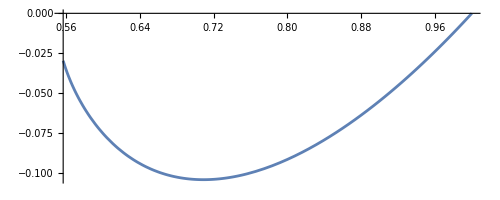

```mathematica
ParametricPlot[{Re[SPoleScalar1[1,0.4,c,0]],Im[SPoleScalar1[1,0.4,c,0]]},{c,0,0.083}]
```

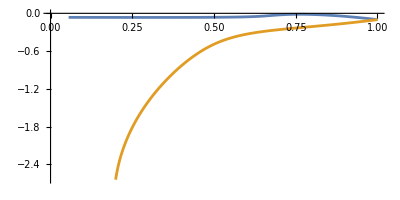

```mathematica
ParametricPlot[{{Re[SPoleScalar0[1,0.4,c,0.1]],Im[SPoleScalar0[1,0.4,c,0.1]]},{Re[SPoleScalar1[1,0.4,c,0.1]],Im[SPoleScalar1[1,0.4,c,0.1]]}},{c,0,0.5},AspectRatio->0.5,ImageSize->Full]
```

```mathematica
PropagatorScalar[s_,M_,m_,c_,c2_]:=1/(s-M^2+c×ScalarMSF0[m,s]+ⅈ×c2);
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

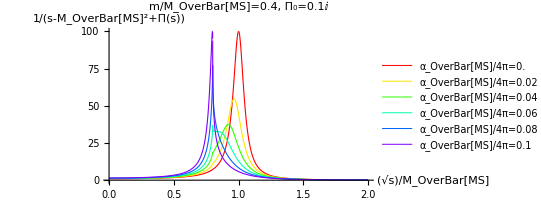

```mathematica
ParametricPlot[Evaluate[Table[{Sqrt[s],Abs[PropagatorScalar[s,1,0.4,0.02n,0.1]]^2},{n,0,5}]],{s,0,4},
PlotStyle->Table[Directive[Hue[1+0.15n],Thickness[0.002]],{n,0,5}],AspectRatio->0.5,ImageSize->Full,PlotRange->Full,MaxRecursion->15,AxesLabel->{Sqrt[s]/Subscript[M, OverBar[MS]],1/(s-Subscript[M, OverBar[MS]]^2+Π[s])},PlotLegends->Placed[Table[StringForm["α_OverBar[MS]/4π=``",0.02n],{n,0,5}],{Right,Top}],PlotLabel->Style["m/M_OverBar[MS]=0.4, Π_0=0.1ⅈ",FontSize->18]]
```

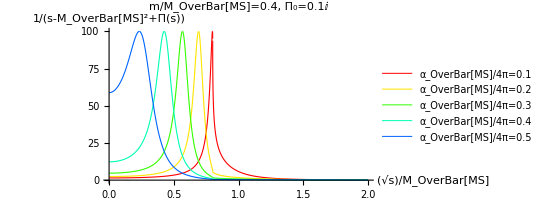

```mathematica
ParametricPlot[Evaluate[Table[{Sqrt[s],Abs[PropagatorScalar[s,1,0.4,0.1+0.1n,0.1]]^2},{n,0,4}]],{s,0,4},
PlotStyle->Table[Directive[Hue[1+0.15n],Thickness[0.002]],{n,0,4}],AspectRatio->0.5,ImageSize->Full,PlotRange->Full,MaxRecursion->15,AxesLabel->{Sqrt[s]/Subscript[M, OverBar[MS]],1/(s-Subscript[M, OverBar[MS]]^2+Π[s])},PlotLegends->Placed[Table[StringForm["α_OverBar[MS]/4π=``",0.1+0.1n],{n,0,4}],{Right,Top}],PlotLabel->Style["m/M_OverBar[MS]=0.4, Π_0=0.1ⅈ",FontSize->18]]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

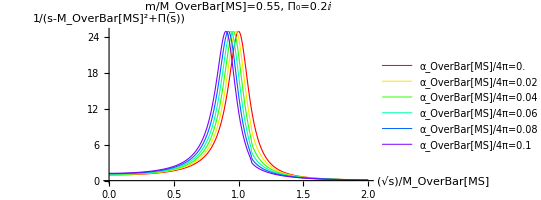

```mathematica
ParametricPlot[Evaluate[Table[{Sqrt[s],Abs[PropagatorScalar[s,1,0.55,0.02n,0.2]]^2},{n,0,5}]],{s,0,4},
PlotStyle->Table[Directive[Hue[1+0.15n],Thickness[0.002]],{n,0,5}],AspectRatio->0.5,ImageSize->Full,PlotRange->Full,MaxRecursion->15,AxesLabel->{Sqrt[s]/Subscript[M, OverBar[MS]],1/(s-Subscript[M, OverBar[MS]]^2+Π[s])},PlotLegends->Placed[Table[StringForm["α_OverBar[MS]/4π=``",0.02n],{n,0,5}],{Right,Top}],PlotLabel->Style["m/M_OverBar[MS]=0.55, Π_0=0.2ⅈ",FontSize->18]]
```

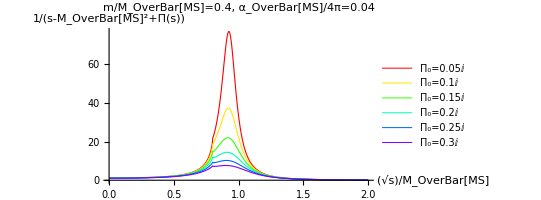

```mathematica
ParametricPlot[Evaluate[Table[{Sqrt[s],Abs[PropagatorScalar[s,1,0.4,0.04,0.05+0.05n]]^2},{n,0,5}]],{s,0,4},
PlotStyle->Table[Directive[Hue[1+0.15n],Thickness[0.002]],{n,0,5}],AspectRatio->0.5,ImageSize->Full,PlotRange->Full,MaxRecursion->15,AxesLabel->{Sqrt[s]/Subscript[M, OverBar[MS]],1/(s-Subscript[M, OverBar[MS]]^2+Π[s])},PlotLegends->Placed[Table[StringForm["Π_0=``ⅈ",0.05+0.05n],{n,0,5}],{Right,Top}],PlotLabel->Style["m/M_OverBar[MS]=0.4, α_OverBar[MS]/4π=0.04",FontSize->18]]
```

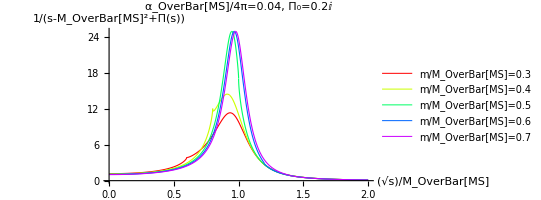

```mathematica
ParametricPlot[Evaluate[Table[{Sqrt[s],Abs[PropagatorScalar[s,1,0.3+0.1n,0.04,0.2]]^2},{n,0,4}]],{s,0,4},
PlotStyle->Table[Directive[Hue[1+0.2n],Thickness[0.002]],{n,0,4}],AspectRatio->0.5,ImageSize->Full,PlotRange->Full,MaxRecursion->15,AxesLabel->{Sqrt[s]/Subscript[M, OverBar[MS]],1/(s-Subscript[M, OverBar[MS]]^2+Π[s])},PlotLegends->Placed[Table[StringForm["m/M_OverBar[MS]=``",0.3+0.1n],{n,0,4}],{Right,Top}],PlotLabel->Style["α_OverBar[MS]/4π=0.04, Π_0=0.2ⅈ",FontSize->18]]
```

```mathematica
FermionMSF0[m_,s_]:=((4 m^2-s)^(3/2))/(3 √s)ArcTan[(√s)/(√(4 m^2-s))]-5 m^2+s+(6 m^2-s)Log[m];
FermionMSF1[m_,s_]:=-((4 m^2-s)^(3/2))/(3 √s)(ArcTan[-(√s)/(√(4 m^2-s))]+π)-5 m^2+s+(6 m^2-s)Log[m];
```

```mathematica
InitialGuessSPFermion0[M_,m_,c_,c2_]:=M^2-c×FermionMSF0[m,M^2]-ⅈ×c2;
InitialGuessSPFermion1[M_,m_,c_,c2_]:=M^2-c×FermionMSF1[m,M^2]-ⅈ×c2;
SPoleFermion0Aux[M_,m_,c_,c2_,IG_?NumericQ]:=s/.FindRoot[s-M^2+c×FermionMSF0[m,s]+ⅈ×c2,{s,IG}];
SPoleFermion1Aux[M_,m_,c_,c2_,IG_?NumericQ]:=s/.FindRoot[s-M^2+c×FermionMSF1[m,s]+ⅈ×c2,{s,IG}];
SPoleFermion0[M_,m_,c_,c2_]:=SPoleFermion0Aux[M,m,c,c2,InitialGuessSPFermion0[M,m,c,c2]];
SPoleFermion1[M_,m_,c_,c2_]:=SPoleFermion1Aux[M,m,c,c2,InitialGuessSPFermion1[M,m,c,c2]];
```

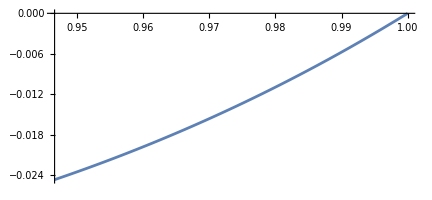

```mathematica
ParametricPlot[{Re[SPoleFermion1[1,0.4,c,0]],Im[SPoleFermion1[1,0.4,c,0]]},{c,0,0.5}]
```

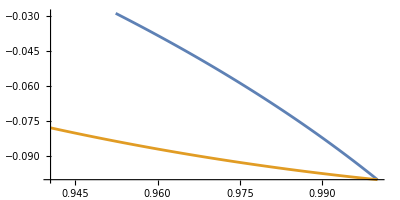

```mathematica
ParametricPlot[{{Re[SPoleFermion0[1,0.4,c,0.1]],Im[SPoleFermion0[1,0.4,c,0.1]]},{Re[SPoleFermion1[1,0.4,c,0.1]],Im[SPoleFermion1[1,0.4,c,0.1]]}},{c,0,0.5},AspectRatio->0.5,ImageSize->Full]
```

```mathematica
PropagatorFermion[s_,M_,m_,c_,c2_]:=1/(s-M^2+c×FermionMSF0[m,s]+ⅈ×c2);
```

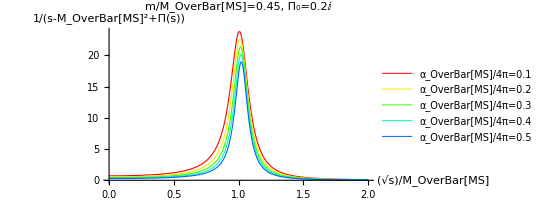

```mathematica
ParametricPlot[Evaluate[Table[{Sqrt[s],Abs[PropagatorFermion[s,1,0.45,0.1+0.1n,0.2]]^2},{n,0,4}]],{s,0,4},
PlotStyle->Table[Directive[Hue[1+0.15n],Thickness[0.002]],{n,0,4}],AspectRatio->0.5,ImageSize->Full,PlotRange->Full,MaxRecursion->15,AxesLabel->{Sqrt[s]/Subscript[M, OverBar[MS]],1/(s-Subscript[M, OverBar[MS]]^2+Π[s])},PlotLegends->Placed[Table[StringForm["α_OverBar[MS]/4π=``",0.1+0.1n],{n,0,4}],{Right,Top}],PlotLabel->Style["m/M_OverBar[MS]=0.45, Π_0=0.2ⅈ",FontSize->18]]
```

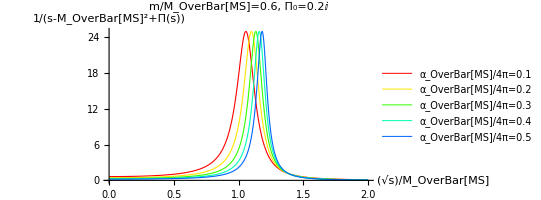

```mathematica
ParametricPlot[Evaluate[Table[{Sqrt[s],Abs[PropagatorFermion[s,1,0.6,0.1+0.1n,0.2]]^2},{n,0,4}]],{s,0,4},
PlotStyle->Table[Directive[Hue[1+0.15n],Thickness[0.002]],{n,0,4}],AspectRatio->0.5,ImageSize->Full,PlotRange->Full,MaxRecursion->15,AxesLabel->{Sqrt[s]/Subscript[M, OverBar[MS]],1/(s-Subscript[M, OverBar[MS]]^2+Π[s])},PlotLegends->Placed[Table[StringForm["α_OverBar[MS]/4π=``",0.1+0.1n],{n,0,4}],{Right,Top}],PlotLabel->Style["m/M_OverBar[MS]=0.6, Π_0=0.2ⅈ",FontSize->18]]
```

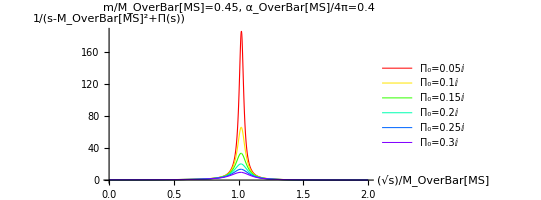

```mathematica
ParametricPlot[Evaluate[Table[{Sqrt[s],Abs[PropagatorFermion[s,1,0.45,0.4,0.05+0.05n]]^2},{n,0,5}]],{s,0,4},
PlotStyle->Table[Directive[Hue[1+0.15n],Thickness[0.002]],{n,0,5}],AspectRatio->0.5,ImageSize->Full,PlotRange->Full,MaxRecursion->15,AxesLabel->{Sqrt[s]/Subscript[M, OverBar[MS]],1/(s-Subscript[M, OverBar[MS]]^2+Π[s])},PlotLegends->Placed[Table[StringForm["Π_0=``ⅈ",0.05+0.05n],{n,0,5}],{Right,Top}],PlotLabel->Style["m/M_OverBar[MS]=0.45, α_OverBar[MS]/4π=0.4",FontSize->18]]
```

Power::infy: Infinite expression 1/(√0.) encountered.

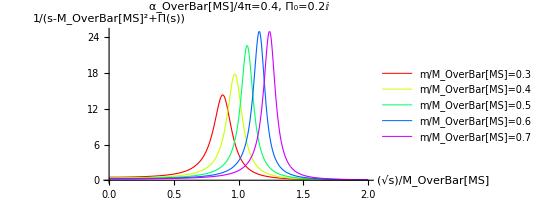

```mathematica
ParametricPlot[Evaluate[Table[{Sqrt[s],Abs[PropagatorFermion[s,1,0.3+0.1n,0.4,0.2]]^2},{n,0,4}]],{s,0,4},
PlotStyle->Table[Directive[Hue[1+0.2n],Thickness[0.002]],{n,0,4}],AspectRatio->0.5,ImageSize->Full,PlotRange->Full,MaxRecursion->15,AxesLabel->{Sqrt[s]/Subscript[M, OverBar[MS]],1/(s-Subscript[M, OverBar[MS]]^2+Π[s])},PlotLegends->Placed[Table[StringForm["m/M_OverBar[MS]=``",0.3+0.1n],{n,0,4}],{Right,Top}],PlotLabel->Style["α_OverBar[MS]/4π=0.4, Π_0=0.2ⅈ",FontSize->18]]
```

```mathematica
TimePropagatorScalar[t_,pMax_,M_,m_,c_,c2_]:=NIntegrate[2Cos[p×t]PropagatorScalar[p^2,M,m,c,c2],{p,0,pMax},WorkingPrecision->MachinePrecision,MaxRecursion->Infinity]
TimePropagatorScalarBranch[t_,pMax_,M_,m_,c_,c2_]:=NIntegrate[2Exp[-ⅈ×p×t]Im[PropagatorScalar[p^2,M,m,c,c2]],{p,4 m^2,pMax},WorkingPrecision->MachinePrecision,MaxRecursion->Infinity]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

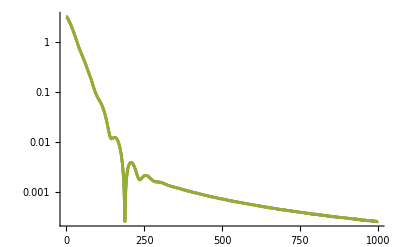

```mathematica
LogPlot[{Abs[TimePropagatorScalar[t,20,1,4/10,4/100,0]],Abs[TimePropagatorScalarBranch[t,20,1,4/10,4/100,0]],Abs[TimePropagatorScalarBranch[t,40,1,4/10,4/100,0]]},{t,0,1000}]
```

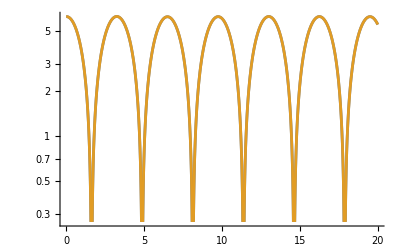

```mathematica
LogPlot[{Abs[ContourIntegrate[2Cos[p×t]PropagatorScalar[p^2,1,6/10,4/100,0],p∈Circle[{1,0},0.1],WorkingPrecision->MachinePrecision]+TimePropagatorScalarBranch[t,20,1,6/10,4/100,0]],Abs[ContourIntegrate[2Cos[p×t]PropagatorScalar[p^2,1,6/10,4/100,0],p∈Circle[{1,0},0.1],WorkingPrecision->MachinePrecision]+TimePropagatorScalarBranch[t,40,1,6/10,4/100,0]]},{t,0,20}]
```

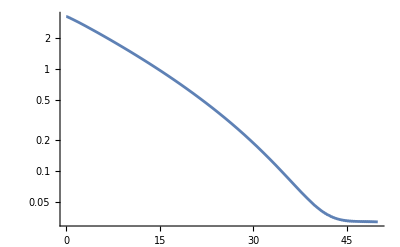

```mathematica
LogPlot[Abs[TimePropagatorScalar[t,20,1,4/10,4/100,1/10]],{t,0,50}]
```

```mathematica
PropagatorScalarExact[s_,M_,m_,c_,c2_]:=1/(s-M^2+c×ScalarMSF0[m,s]+c2/π×Log[-1/s]);
TimePropagatorScalarExact[t_,pMax_,M_,m_,c_,c2_]:=NIntegrate[2Cos[p×t]PropagatorScalarExact[p^2,M,m,c,c2],{p,0,pMax},MaxRecursion->Infinity]
TimePropagatorScalarExactBranch[t_,pMax_,M_,m_,c_,c2_]:=NIntegrate[2Exp[-ⅈ×p×t]Im[PropagatorScalarExact[p^2,M,m,c,c2]],{p,0,pMax},MaxRecursion->Infinity]
```

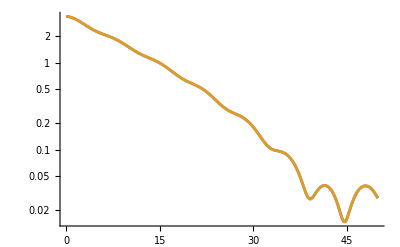

```mathematica
LogPlot[{Abs[TimePropagatorScalarExact[t,20,1,4/10,4/100,1/10]],Abs[TimePropagatorScalarExactBranch[t,20,1,4/10,4/100,1/10]]},{t,0,50}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

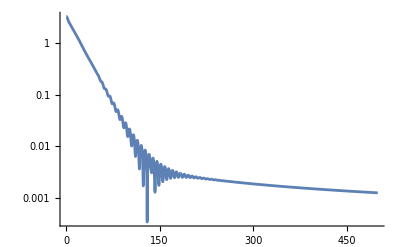

```mathematica
LogPlot[Abs[TimePropagatorScalarExact[t,10000,1,1,0,1/10]],{t,0,500},PlotRange->Full,MaxRecursion->15,ImageSize->Full]
```